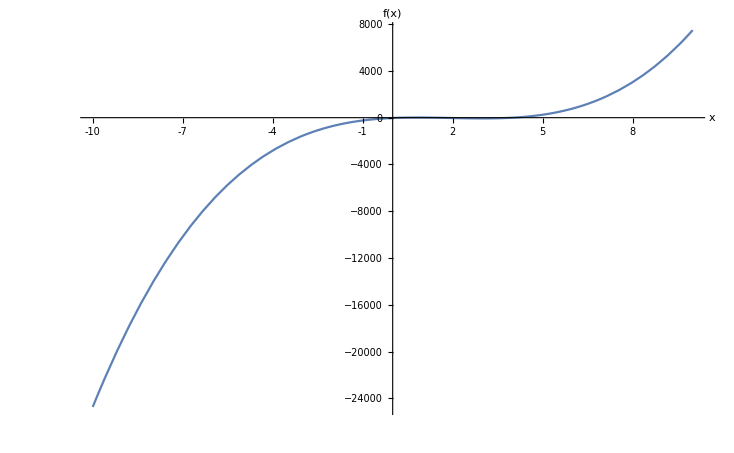

```mathematica
(* 221701 Сковлюк Г.Р.   Вариант 4*)

(* 1) *)

f[x_]:= 15 x^3-86 x^2+111x-28
Plot[f[x],{x,-10,10},AxesLabel->{"x","f(x)"},Ticks->{Range[-10,10],Automatic}]
```

```mathematica
x0= -1;
x1 =2;
ϵ=10^-3;
xnew=x1-(f[x1](x1-x0))/(f[x1]-f[x0]);
i=0;

While[Abs[xnew-x1]>ϵ,x0=x1;
x1=xnew;
xnew=x1-(f[x1](x1-x0))/(f[x1]-f[x0]);
i++;]
Print["Количество итераций - ",i,"  Корень - ",N[xnew]]
```

Количество итераций - 4  Корень - 1.4

```mathematica
Clear[x,f,xnew,x0,x1,i]
```

```mathematica
(* 2) *)

f=x^6+6 x^5+12 x^4+6 x^3-9 x^2-12x-4
```

-4-12 x-9 x^2+6 x^3+12 x^4+6 x^5+x^6

```mathematica
Print["Корни "]
N[solutions=Solve[f==0,x],2]
N[numerical=NSolve[f==0,x],2]
Roots[f==0,x]
FindRoot[f==0,{x,1}]
Print["Разложение  ",Factor[f]]
```

Корни

{{x→-2.},{x→-2.},{x→-1.},{x→-1.},{x→-1.},{x→1.}}

{{x→-2.},{x→-2.},{x→-1.},{x→-1.},{x→-1.},{x→1.}}

x==-2||x==-2||x==-1||x==-1||x==-1||x==1

{x→1.}

Разложение  (-1+x) (1+x)^3 (2+x)^2

```mathematica
Clear[x,f]
```

```mathematica
(* 3) *)
```

-2+3^x-4 x

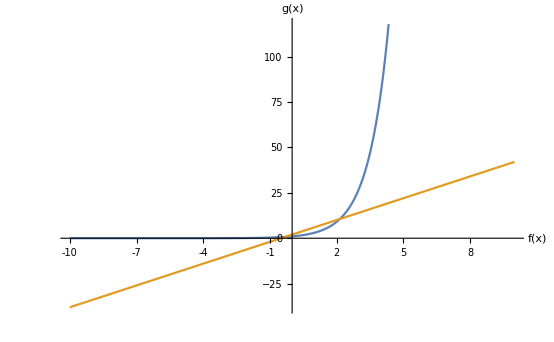

```mathematica
f[x_]:=3^x-4x-2
Subscript[f, 0]=3^x-4x-2
h[x_]:=3^x
g[x_]:=4x+2
Plot[{h[x],g[x]},{x,-10,10},AxesLabel->{"f(x)","g(x)"},Ticks->{Range[-10,10],Automatic}]
```

```mathematica
Print["Корень  ",N[solutions=FindRoot[Subscript[f, 0]==0,{x,-4}]]]
```

Корень  {x→-0.325081}

```mathematica
x0=-1;
maxi=100;
ϵ=10^-3;
iter=0;
x=x0;
For[i=1,i<=maxi,i++,
df:=D[f[y],y];
If[df/.y->x==0,Break[]];

xnew=y-f[y]/df/.y->x;
If[Abs[xnew-x]<ϵ, iter=i; x=xnew;Break[]];
x=xnew;
]

Print["Количество итераций - ",i,"  Корень - ",N[xnew]]
```

Количество итераций - 3  Корень - -0.325081

```mathematica
x=x0;
xprev=x0-0.1;
iter=0;
For[i=1,i<=maxi,i++,df:=(f[y]-f[xprev])/(y-xprev);
If[df/.y->x==0,Break[]];
xnew=x-f[x]/df/.y->x;
If[Abs[xnew-x]<ϵ,
iter=i;
x=xnew;
Break[]];
xprev=x;
x=xnew;
]
Print["Количество итераций - ",i,"  Корень - ",N[xnew]]
```

Количество итераций - 4  Корень - -0.325081

```mathematica
(*  4)  *)

x0=-1;
g[x_]:=x+0.1*f[x]
ϵ=10^-3;
maxi=100;
x=x0;
i=0;
While[i<=maxi,xnext=g[x];If[Abs[xnext-x]<ϵ,Break[],x=xnext];
i++;
]
Print["Количество итераций - ",i,"  Корень - ",N[xnew]]
```

Количество итераций - 14  Корень - -0.325081

```mathematica
Clear[x,f,g,h]
```

```mathematica
(*  5)  *)
```

```mathematica
h=3^x;
g=4x+2;
```

```mathematica
NSolve[h==g,x_]
Solve[h==g,x_]
FindRoot[h==g,{x,-1}]
```

{}

{}

{x→-0.325081}

```mathematica
Print ["Решено с помощью FindRoot  ",FindRoot[h==g,{x,-1}]]
```

Решено с помощью FindRoot  {x→-0.325081}

```mathematica
Clear[x,f,g,h]
```

```mathematica
(*  6)  *)
```

```mathematica
f[x_,y_]=(x^2)^(1/3)+(y^2)^(1/3)-25^(1/3);
g[x_,y_]=x^3+y^3-9x*y;
```

```mathematica
gr1=ContourPlot[f[x,y]==0,{x,-7,7},{y,-7,7},Axes->True,Frame->False];
```

```mathematica
gr2=ContourPlot[g[x,y]==0,{x,-7,7},{y,-7,7},Axes->True,Frame->False];
```

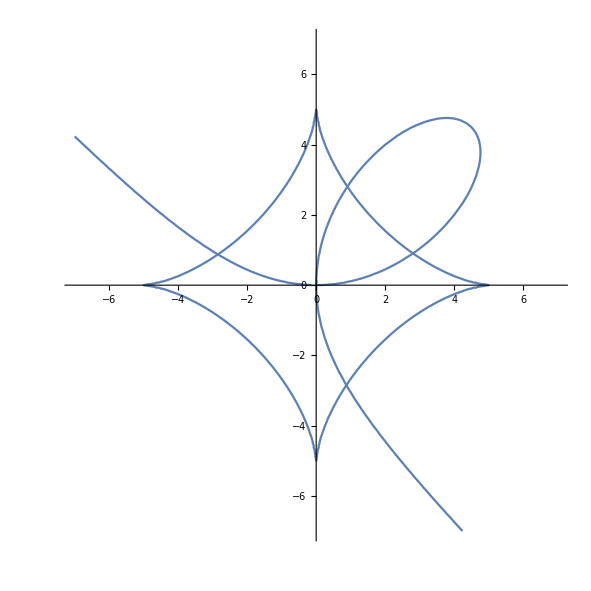

```mathematica
Show[gr1,gr2,ImageSize->Medium]
```

```mathematica
FindRoot[{f[x,y]==0,g[x,y]==0},{x,3},{y,1}]
```

{x→2.80557,y→0.903822}

```mathematica
FindRoot[{f[x,y]==0,g[x,y]==0},{x,1},{y,3}]
```

{x→0.903822,y→2.80557}

```mathematica
FindRoot[{f[x,y]==0,g[x,y]==0},{x,1},{y,-3}]
FindRoot[{f[x,y]==0,g[x,y]==0},{x,-3},{y,1}]
```

{x→0.875031,y→-2.8479}

{x→-2.8479,y→0.875031}